## Setup

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"challenge\\Sample3\\"]];
```

```mathematica
imrows={1,512};
imcols={1,512};
subset=59;
```

### Import

```mathematica
namelist = {"Sample3 Reference","Sample3-001 X0.10 Y0.10 N2 C0 R0"};
imlist=Table[Import[StringJoin[namelist[[ii]],".tif"],"Image"],{ii,Dimensions[namelist][[1]]}];
matlist=Table[Import[StringJoin[namelist[[ii]],".mat"],"LabeledData"],{ii,1,Dimensions[namelist][[1]]}];
```

```mathematica
imref=imlist[[1]];
imdef=imlist[[2]];
```

```mathematica
imsize=ImageDimensions[imref];
flowsize={imcols[[2]]-imcols[[1]]+1,imrows[[2]]-imrows[[1]]+1};
imcenter={Mean[imcols],imsize[[2]]-Mean[imrows]};
imbottomleft={imcols[[1]],imrows[[2]]};
```

#### Compute dense optical flow; default MaxIternations = 10

```mathematica
flow=Table[{0,0},{flowsize[[1]]},{flowsize[[2]]}];
```

```mathematica
dispvals = ImageDisplacements[{ImageTake[imref,imrows,imcols],ImageTake[imdef,imrows,imcols]},MaxIterations->1000];
```

#### Note: number of MaxIterations didn’t make a difference in RMSE

```mathematica
Dimensions[dispvals]
```

{1,512,512,2}

```mathematica
dispfield=dispvals[[1,;;,;;,;;]];
```

```mathematica
Dimensions[dispfield]
```

{512,512,2}

## 2-D displacements, image method

#### Map displacements as rescaled two-channel image

```mathematica
imdisp = Map[Image,Map[Rescale,dispvals]][[1]];
```

#### Map single channel image of horizontal displacement

```mathematica
imu1= Map[Image,dispvals[[;;,;;,;;,1]]][[1]];
```

#### Map single channel image of vertical displacement

```mathematica
imu2= Map[Image,dispvals[[;;,;;,;;,2]]][[1]];
```

```mathematica
overlayopacity=0.75;
```

#### Overlay rescaled two-channel displacement image on reference image

```mathematica
ImageCompose[imref,{imdisp,overlayopacity},imcenter];
```

## 2-D displacements, array method

```mathematica
Dimensions[dispfield[[;;,;;,1]]]
```

{512,512}

```mathematica
ListContourPlot[dispfield[[;;,;;,2]],MaxPlotPoints->30,PlotLegends->Automatic,PlotLabel->"Vertical displacement, upside down from image"];
```

#### Reverse the rows to match image y-axis convention, and apply DataRange to match image coordinates

```mathematica
u1=dispfield[[;;,;;,1]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]];
u2=dispfield[[;;,;;,2]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]];
```

Couldn’t get the overlay opacity directive to work:

```mathematica
(*lp=ListContourPlot[Reverse[u2,1],DataRange->{{imcols[[1]],imcols[[2]]},{imrows[[1]],imrows[[2]]}},MaxPlotPoints->100,PlotLegends->Automatic,ContourStyle->None,ColorFunction->(Directive[Opacity[overlayopacity],ColorData["M10DefaultDensityGradient"][#]]&)];*)
```

```mathematica
lp=ListContourPlot[Reverse[u2,1],DataRange->{{imcols[[1]],imcols[[2]]},{imrows[[1]],imrows[[2]]}},MaxPlotPoints->100,PlotLegends->Automatic,ContourStyle->None,ColorFunction->"FuchsiaTones",ClippingStyle->Automatic,PlotRange->{0,0.05}];
```

```mathematica
Vmap=Show[imref,lp,ImageSize->Medium,PlotLabel->"Vertical displacement"];
```

```mathematica
Export["mathematicaV.png",Vmap]
```

mathematicaV.png

## Stats comparison

```mathematica
vicu=matlist[[2,5,2]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]];
vicv=matlist[[2,6,2]][[(subset+1);;-(subset+1),(subset+1);;-(subset-1)]];
```

```mathematica
Dimensions[vicu]
```

{393,395}

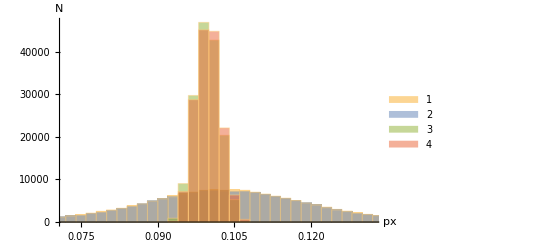

```mathematica
Histogram[{Flatten[u1],-Flatten[u2],Flatten[vicu],Flatten[vicv]},AxesLabel->{"\npx","N"},ChartLegends->Automatic]
```

```mathematica
realval=0.1;
RootMeanSquare[Transpose@{Flatten[u1-realval],Flatten[-u2-realval]}]
RootMeanSquare[Transpose@{Flatten[vicu-realval],Flatten[vicv-realval]}]
```

{0.0194257,0.0196832}

{0.00241598,0.00237105}

```mathematica
vics=Sqrt[vicu^2+vicv^2];
maths=Sqrt[u1^2+u2^2];
```

```mathematica
vicsRMS=RootMeanSquare[Flatten[vics-Sqrt[2]/10]]
mathsRMS=RootMeanSquare[Flatten[maths-Sqrt[2]/10]]
```

0.00253256

0.0201827

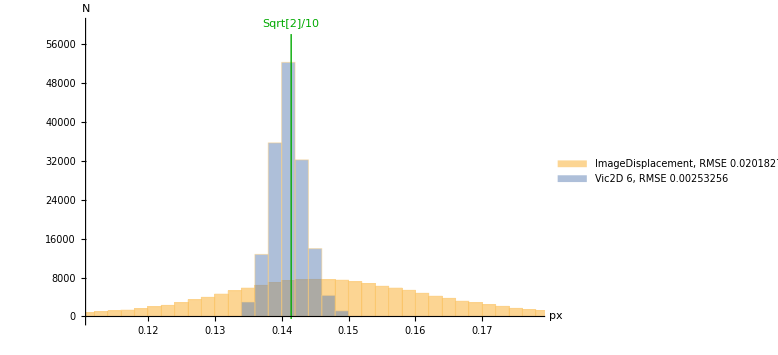

```mathematica
comphisto=Show[Histogram[{Flatten[maths],Flatten[vics]},AxesLabel->{"\npx","N"},ChartLegends->Placed[{StringJoin["ImageDisplacement, RMSE ",ToString[mathsRMS]],StringJoin["Vic2D 6, RMSE ",ToString[vicsRMS]]},Bottom]],Graphics[{Darker[Green],Line[{{Sqrt[2]/10,-500},{Sqrt[2]/10,58000}}],Text["Sqrt[2]/10",{Sqrt[2]/10,60000}]}],ImageSize->Large,BaseStyle->{FontSize->14}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["comphisto.pdf",comphisto];
Export["comphisto.png",comphisto];
```

comphisto.pdf

comphisto.png